```mathematica
FresnelDielectric[ei_,et_,ndi_,ndt_]:=(
rparl=(et*ndi-ei*ndt)/(et*ndi+ei*ndt);
rperp=(ei*ndi-et*ndt)/(ei*ndi+et*ndt);
Return[(rparl^2+rperp^2)/2]
)
FresnelLayer[ei_,et_,cosi_]:=(
eta=ei/et;
sini2=1-cosi^2;
sint2=eta*eta*sini2;
cost=Sqrt[1-sint2];
Return[FresnelDielectric[ei,et,cosi,cost]]
)
```

```mathematica
FresnelShlick[ei_,et_,cosi_]:=(
r0=((ei-et)/(ei+et))^2;
Return[r0+(1-r0)(1-cosi)^5]
)
```

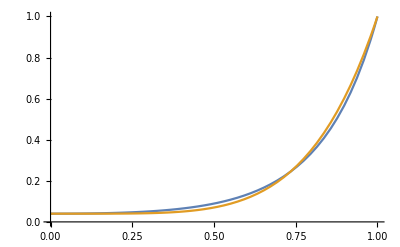

```mathematica
ei=1;
et=1.5;
Plot[{FresnelLayer[ei,et,1-cosi],FresnelShlick[ei,et,1-cosi]},{cosi, 0, 1},PlotRange->{{0, 1},{0,1}}]
```

```mathematica
f=f0+(1-f0)*(1-vh)^5;
f2=f0*(1-(1-vh)^5)+(1-vh)^5
```

0.172111 (1-(1-vh)^5)+(1-vh)^5